```mathematica
(*Vertices of equalateral triangle in the plane*)
p1= {0,0};
p2={1,0};
p3={1/2,Sqrt[3]/2};
fc={1/2, Sqrt[3]/6};
(*Vertices of the face of an icosahedron and its face center*)
m=(1+Sqrt[5])/2; mp=(1-Sqrt[5])/2; fact=Sqrt[-mp Sqrt[5]];
vertex[1]={0,mp,1}/fact; vertex[2]={0,mp,-1}/fact;
vertex[3]={1,0,mp}/fact; vertex[4]={1,0,-mp}/fact;
vertex[5]={mp,1,0}/fact; vertex[6]={mp,-1,0}/fact;
For[k=1,k≤6,k++,
vertex[k+6]=-vertex[k]];
icoVert = Table[vertex[j],{j,1,12}];
v1=icoVert[[1]];
v2=icoVert[[4]];
v3=icoVert[[8]];
vfc ={-mp/Sqrt[3],0,m/Sqrt[3]};
```

```mathematica
testlattice=Import["lattice.dat"];
testmap=Import["quadGrid.dat"];
test8gens=Import["8gen3Dmap.dat"];
```

```mathematica
test8gens3Dlat=Import["8gen3D.dat"];
```

```mathematica
test8genSol=Import["8genQuadSol.dat"];
```

```mathematica
plnp=ListPointPlot3D[{test8gens},PlotStyle->{PointSize[0.0025]},BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False];
plnp3=ListPointPlot3D[{test8gens3Dlat},PlotStyle->{PointSize[0.0075]},BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False];
plnp2=ListPointPlot3D[{test8genSol},PlotStyle->{PointSize[0.0075]},BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False];
plv=ListPointPlot3D[{icoVert[[1]],icoVert[[4]],icoVert[[8]],vfc},PlotStyle->{PointSize[0.02]},BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False];
plsph =Graphics3D[{Sphere[]},Boxed->False];
plt=Show[plsph,plnp,plnp2,plv]
```

-Graphics3D-

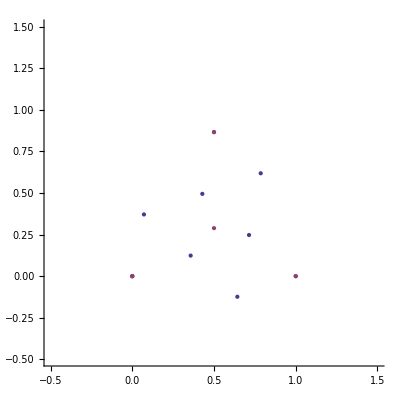

```mathematica
ListPlot[{testlattice,{p1,p2,p3,fc}},PlotRange->{{-1/2,3/2},{-1/2,3/2}},AspectRatio->1]
```

```mathematica
test8gens
test8gens3Dlat
```

{{0.236531,-0.403501,0.883878},{0.315838,-0.257049,0.91333},{0.375004,-0.098491,0.921776},{0.463467,-0.238117,0.853522},{0.524428,-0.0667537,0.848834},{0.603343,-0.212147,0.768747},{0.653969,-0.0420376,0.755353},{0.762751,-0.0209419,0.646353}}

{{0.221471,-0.404088,0.887504},{0.300929,-0.247056,0.921089},{0.36752,-0.0903998,0.925612},{0.45671,-0.232833,0.858607},{0.513273,-0.0696532,0.855394},{0.606804,-0.2107,0.766417},{0.64874,-0.0464183,0.759593},{0.763005,-0.0225762,0.645998}}

```mathematica
sphercoords=CoordinatesFromCartesian[#,Spherical]& /@  test8gens
```

{{1.,0.486707,-1.04059},{1.,0.419408,-0.683137},{1.,0.398159,-0.256839},{1.,0.54809,-0.474605},{1.,0.55702,-0.126608},{1.,0.693917,-0.338116},{1.,0.714604,-0.0641925},{1.,0.868001,-0.0274489}}